```mathematica
ComputeRandomVarData[distribution_,mean_,sdev_]:=Block[{p1,p2,case},
case=distribution;
Switch[case
,"NORMAL",
p1=mean;
p2=sdev;
case=1;
,"LOGNORMAL",
p2=√Log[1+(sdev/mean)^2];
p1=Log[mean ]-0.5 p2^2;
case=2;
,"DETERM",
p2=0;
p1=mean ;
case=3;
,"UNIFORME",
p1=1/2 (1+2 mean-√(1+12 sdev^2));
p2=1/2 (-1+2 mean+√(1+12 sdev^2));
case=4;
];
{mean,sdev,p1,p2,case}
];
PHI[x_]:=CDF[NormalDistribution[0,1],x];
InvPHI[x_]:=InverseCDF[NormalDistribution[0,1],x];
phi[x_]:=PDF[NormalDistribution[0,1],x];
ComputeY[RvVec_,Nsamples_]:=Block[{y,x,nrv,i,j,mu,sig,p1,p2,case},
nrv=Length[RvVec];
y=Table[0,{nrv}];
For[j=1,j≤nrv,j++,
{mu,sig,p1,p2,case}=RvVec[[j]];
y[[j]]=RandomVariate[NormalDistribution[0,1],Nsamples];
];
Transpose[y]
]
FromYtoZ[y_,Rx_]:=Block[{x,sz,i,j,var,z,Jyz,Jzy},
sz=Length[y];
{Jzy,Jyz} = ComputeJYZ[Rx];
z=Table[0,{sz}];
For[j=1,j≤sz,j++,
z[[j]]=Jyz.y[[j]];
];
z
];
FromZtoX[RvVec_,z_]:=Block[{x,sz,i,j,JXZ,JZX,MuNeqEquiv,rv,nrv,mu,sig,p1,p2,case,Fx,fx,hx},
sz=Length[z];
nrv=Length[RvVec];
x=Table[0,{sz},{nrv}];
fx=Table[0,{sz},{nrv}];
hx=Table[0,{sz},{nrv}];
For[j=1,j≤sz,j++,
For[i=1,i≤nrv,i++,
{mu,sig,p1,p2,case}=RvVec[[i]];
If[case==1,
x[[j,i]]=z[[j,i]] p2+p1 ;
];
If[case==2,
x[[j,i]]=Exp[z[[j,i]] p2+p1];
];
If[case==3,
x[[j,i]]=z[[j,i]]p1;
];
If[case==4,
Fx=CDF[UniformDistribution[{p1,p2}],z[[j,i]]];
x[[j,i]]=(p2-p1)*Fx+p1;
];
If[case≠1 && case≠2 && case≠4 && case≠3,
Print["Error Distribution not Implemented!"];
];
fx[[j,i]]=f[RvVec[[i]],x[[j,i]]];
hx[[j,i]]=phi[x[[j,i]]];
];
];
{x,fx,hx}
];
F[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case,Fx},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
Fx=CDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
Fx=CDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
Fx=If[x≥ p1,1.0,0];
,4,(*Uniforme*)
Fx=CDF[UniformDistribution[{p1,p2}],x];
(*Fx=If[x≥ p2,1.0,If[x≤ p1,0.0,(x-p1)/(p2-p1)]];*)
];
Fx
];
f[RandonVar_,x_]:=Block[{fx,mu,sig,p1,p2,case},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
fx=PDF[NormalDistribution[mu,sig],x];
,2,(*LogNormal*)
fx=PDF[LogNormalDistribution[mu,sig],x];
,3,(*Deterministico*)
fx=If[x≥ 1.05 p1,0.0,If[x≤ 0.95 p1,0.0,10]]
,4,(*Uniforme*)
fx=PDF[UniformDistribution[{p1,p2}],x];
];
fx
];
ComputeXZ[RandonVar_,x_]:=Block[{mu,sig,z,SdevNeq,case,MuNeq,p1,p2},
{mu,sig,p1,p2,case}=RandonVar;
Switch[case
,1,(*Normal*)
SdevNeq=sig;
MuNeq=mu;
,2,(*LogNormal*)
SdevNeq=x p2;
MuNeq=x*(1-Log[x]+p1);
,3,(*Deterministico*)
SdevNeq=1;
MuNeq=mu;
,4,(*Uniforme*)
z=InvPHI[F[RandonVar,x]];
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
,5,(*Geral*)
z=InvPHI[F[RandonVar,x]];
SdevNeq=phi[z]/f[RandonVar,x];
MuNeq=x-z SdevNeq;
];
{SdevNeq,MuNeq}
];
ComputeJXZ[RandonVarVec_,x_]:=Block[{sz,i,j,JXZ,JZX,MuNeq,SdevNeq,MuNeqEquiv,Mean},
sz=Length[RandonVarVec];
JXZ=Table[0,{sz},{sz}];
JZX=Table[0,{sz},{sz}];
MuNeqEquiv=Table[0,{sz}];
Mean=Table[0,{sz}];
For[i=1,i≤sz,i++,
{SdevNeq,MuNeq}=ComputeXZ[RandonVarVec[[i]],x[[i]]];
JXZ[[i,i]]=SdevNeq;
JZX[[i,i]]=1/SdevNeq;
MuNeqEquiv[[i]]=MuNeq;
];
{JXZ,JZX,MuNeqEquiv}
];
ComputeJYZ[RX_]:=Block[{cx,L,correlated,Jyz,Jzy,NRV},
NRV=Length[RX];
If[Det[RX]≠1,
L=Transpose[CholeskyDecomposition[RX]];
Jyz=Inverse[L];
Jzy=L;
If[Det[(L.Transpose[L])-RX]> 10^-8,Print["Attention, Cholesky decomposition failed!"]];
,
Jyz=IdentityMatrix[NRV];
Jzy=IdentityMatrix[NRV];
];
Return[{Jyz,Jzy}];
];
MeritFunction[GX_,y_,Jxy_,Mneq_,c_]:= Block[{x},
(y.y)/2+c Abs[GX[Jxy.y+Mneq]]
];
ComputeC[y_,grady_,dk_,g_]:= Block[{c,eta=2},
If[Abs[g]<10^-8,
c = eta
,
c=eta Abs[1/g(y.grady)/(grady.grady)]
];
c
];
PenalizeXhalf[x1_,x2_,Xmax_,Xmin_]:=Block[{xpen,Penalized,PenalSteps,sz,a,b,i,counter},
 xpen = x2;
sz=Length[x1];
counter=1;
For[i=1,i≤ sz,i++,
While[xpen[[i]]≥ Xmax[[i]] && counter≤1000,
xpen[[i]] = (xpen[[i]]+x1[[i]])/2; 
counter++;
];
counter=1;
While[xpen[[i]]≤ Xmin[[i]] && counter<=1000,
xpen[[i]] = (xpen[[i]]+x1[[i]])/2; 
counter++;
];
];

xpen
];
ComputeExtremes[RandonVar_]:=Block[{xmax,xmin,mu,sig,p1,p2,case },
{mu,sig,p1,p2,case}=RandonVar;

If[case≠4,(*se for diferente de uniforme*)
xmax=mu+3sig;
xmin=mu-3sig;
,
xmin=p1;
xmax=p2;
];
{xmax,xmin}
];
ArmijoLineSearch[GX_,y_,grady_,Jxy_,Mneq_,dk_,kprev_]:=Block[{gx,c,kk,My,a=0.1,b=0.5,k,kmax=30,gradMtimesD,A,BB,B,gy,an,an1,tolerance=10^-5},
k=kprev;
gy=GX[y];
gx=GX[Jxy.y+Mneq];
c=ComputeC[y,grady,dk,gx];
gradMtimesD = (y+c Sign[gy]grady).dk;
My = MeritFunction[GX,y,Jxy,Mneq,c];
A=MeritFunction[GX,y+b^k dk ,Jxy,Mneq,c];
B=My+a b^k gradMtimesD;
While[k≤kmax&&A>B,
A=MeritFunction[GX,y+b^k dk ,Jxy,Mneq,c];
B=My+a b^k gradMtimesD;
k++;
];
If[k>=kmax, 
Return[{-2,1}];
,
Return[{k,b^k}];
];
];
FromXtoY[RvVec_,x_,Jyz_,Jzy_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,y},
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
y=Jyx.(x-Mneq);
{y,Jxy,Mneq}
];
FromYtoX[RvVec_,y_,Rx_]:=Block[{Jzx,Jxz,Jxy,Jyx,Mneq,x,Jyz,Jzy},
{Jyz,Jzy} =ComputeJYZ[Rx];
{Jxz,Jzx,Mneq} =  ComputeJXZ[RvVec,x];
Jyx = Jzy.Jzx;
Jxy = Jxz.Jyz;
x=Jxy.y+Mneq;
{x,Jyx,Mneq}
];
HRLF[Gx_,Gradx_,RvVec_,Rx_]:=Block[{i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=200,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alpha,xn,xmax,xmin,nrv,PostProcess={},post=True,Sdev,DistribCases,Mean},
k=1;
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0,{nrv}];
xmin=Table[0,{nrv}];
For[i=1,i≤nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
k=1;
betan=0;
While[checkconv>tol &&k< NmaxIT,
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | y = ",y ];*)
grady=Transpose[Jxy].Gradx[x];
y=((grady.y)-g)/(grady.grady)grady;
x=Jxy.y+Mneq;
(*Print["*****"];
xn=Jxy.y+Mneq;
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];
x=PenalizeXhalf[x,xn,xmin,xmax];
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];*)
If[post==True,
AppendTo[PostProcess,x];
];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
betan1=Norm[y];
checkconv=Abs[betan1-betan];
betan=betan1;
k++;
];
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g], "  | y = ",y ];*)
alpha=( grady/(√(grady.grady)))^2;
(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];*)
(*Print[TableForm[{{"X"," β ", "PF", "Y "," α "},{x,betan,PHI[-betan] ,y,alpha}}]];*)
(*Print[TableForm[{{" X1 "," X2 ", " X3 ", " PF "," β "},{x[[1]],x[[2]],x[[3]],PHI[-betan],betan}}]];*)
{x[[1]],x[[2]],x[[3]],betan,g}
];
iHRLF[Gx_,Gradx_,RvVec_,Rx_]:=Block[{i,y0,Mneq,x,y,g,gradx,grady,betan,betan1,k,checkconv=1,tol=10^-3,NmaxIT=200,Jyz,Jzy,Jzx,Jxz,Jxy,Jyx,alfa,dk,c,sensivity,kn,kn1,post=True,PostProcess,xn,xmax,xmin,nrv,Sdev,DistribCases,Mean},
k=1;
Mean=Transpose[RvVec][[1]];
x=Mean;
Sdev=Transpose[RvVec][[2]];
DistribCases=Transpose[RvVec][[5]];
nrv=Length[RvVec];
xmax=Table[0,{nrv}];
xmin=Table[0,{nrv}];
For[i=1,i≤nrv,i++,
{xmax[[i]],xmin[[i]]}=ComputeExtremes[RvVec[[i]]];
];
{Jzy,Jyz}  = ComputeJYZ[Rx];
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
k=1;
betan=0;
alfa=1;
kn=0;
kn1=0;
alfa=1;
If[post==True,
PostProcess={};
];
xn=x;
(*Print["x0 = ",xn];*)
While[checkconv>tol &&k< NmaxIT,
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",N[g] ," | alfa = ",alfa, "| kn = ",kn];*)
grady=Transpose[Jxy].Gradx[x];
dk=(((grady.y)-g)/(grady.grady)grady)-y;
{kn1,alfa}=ArmijoLineSearch[Gx,y,grady,Jxy,Mneq,dk,kn];
kn=kn1;
y+=alfa dk;
xn=Jxy.y+Mneq;
x=PenalizeXhalf[x,xn,xmax,xmin];
(*Print["*****"];
xn=Jxy.y+Mneq;
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];
x=PenalizeXhalf[x,xn,xmin,xmax];
Print["xmin = ",xmin, " xmax = ",xmax, " x = ",x , " xn = ",xn];*)
(*If[post==True,
AppendTo[PostProcess,x];
];*)
{y,Jxy,Mneq}=FromXtoY[RvVec,x,Jyz,Jzy];
g=Gx[x];
betan1=Norm[y];
checkconv=Abs[betan1-betan];
betan=betan1;
k++;
];
(*Print[ " | iter = ",k,"  | residual = ",checkconv," | G(x) = ",g ," | alfa = ",alfa, "| kn = ",kn];*)
sensivity=( grady/(√(grady.grady)))^2;
(*Print[" SOLUTION "];
Print[" x = ",x];
Print[" β = ",betan];
Print[ " Pf = ",PHI[-betan] ];
Print[TableForm[{{" Y "," sensivity "},{y,sensivity}}]];*)
{x[[1]],x[[2]],x[[3]],betan,g}
];
MonteCarlo[RvVec_,Nsamples_,RX_,GX_]:=Block[{y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,vartemp},
y=ComputeY[RvVec,Nsamples];
z=FromYtoZ[y,RX];
{x,fx,hx}=FromZtoX[RvVec,z];

PostProc=Table[0,{Nsamples},{2}];
counter=0;
vartemp=0;
For[i=1,i≤Nsamples,i++,
(*Print["fx = ",fx[[i]]];
Print["hx = ",hx[[i]]];
Print["hx/fx = ",hx[[i]]/fx[[i]]];*)
If[GX[x[[i]]]≤0,
(*vartemp=fx[[i]]/hx[[i]];*)
AppendTo[xfailed,x[[i]]];
counter++;
];

PostProc[[i,1]]=i;
beta=-InvPHI[N[counter/Nsamples]];
PostProc[[i,2]]=beta;
];
Print["Counter = ",counter];
Pf=N[counter/Nsamples];
Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];
{PostProc,x,xfailed,beta}
];

(*ImportanceMonteCarlo[RvVec_,Nsamples_,RX_,GX_]:=Block[{y,z,x,counter,Pf,beta,i,PostProc,xfailed={},fx,hx,sum,j},
y=ComputeY[RvVec,Nsamples];
z=FromYtoZ[y,RX];
{x,fx,hx}=FromZtoX[RvVec,z];
PostProc=Table[0,{Nsamples},{2}];
counter=0;
sum=0;
For[i=1,i≤Nsamples,i++,
For[j=1,j≤ Length[RvVec],j++,
sum+=fx[[i,j]]/hx[[i,j]];
];
];
Pf=sum;
beta=-InvPHI[Pf];
Print["Pf Crude Monte Carlo  = ",Pf];
Print["β Crude Monte Carlo = ",beta];
];*)
```

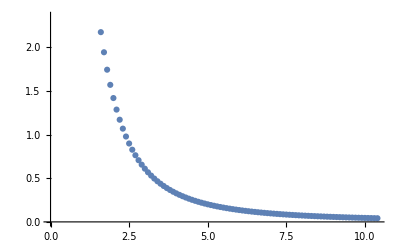

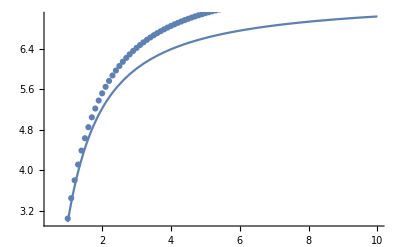

```mathematica
lambda=0.6;
sollambbeta={};
soldbetalambda={};
sols={};
GX[{X1_,X2_,X3_}] := lambda X1 X2- X3;
GRADX[{X1_,X2_,X3_}]:={lambda X2,lambda X1,-1};
(* Create Random Variables *)
RVVec={
ComputeRandomVarData["NORMAL",40.,5.]
,ComputeRandomVarData["NORMAL",50.,2.5]
,ComputeRandomVarData["NORMAL",1000.,200.]
};
RX=IdentityMatrix[Length[RVVec]];
steps=100;
betavec=Table[0,{steps}];
lambdavec=Table[0,{steps}];
dbetaL=0;
For[i=1,i<steps,i++,
sol=HRLF[GX,GRADX,RVVec,RX];
(*Nsamples=10000;
{post,randonSamples,failed,beta}=MonteCarlo[RVVec,Nsamples,RX,GX];*)
betavec[[i]]=sol[[4]];
lambdavec[[i]]=lambda;
If[i≠1,
dbetaL=(betavec[[i]]-betavec[[i-1]])/(lambdavec[[i]]-lambdavec[[i-1]]);
AppendTo[soldbetalambda,{lambda,dbetaL}];

];
AppendTo[sols,{lambda,sol[[4]]}];
lambda+=0.1;
];
betalamb[l_]:=(-1000+2000 l)/(√(40000+72500. l^2))
pll=Plot[betalamb[x],{x,0.5,10}];
pllll=ListPlot[sols];
plll=ListPlot[soldbetalambda]
Show[pll,pllll]
```

```mathematica
RIA[GX_,GRADX_,RVVec_,RX_,lambda0_,lambda1_,betatarget_,varvec_]:=Block[{i,varveccopy,varvecinternal,GXinternal,GRADXinternal,tol=10^-3,a,b,mu,lambda,erro,eps,sol,f1,f2,maxcounter=50,k=1},
eps=tol/10;
a=lambda0;
b=lambda1;
lambda=(a+b)*0.5-eps;
mu=(a+b)*0.5+eps;
erro =2*tol+1;
varveccopy=Table[0,Length[varvec]];
For[i=1,i≤Length[varvec],i++,varveccopy[[i]]=varvec[[i]]];
varvecinternal=Table[0,Length[varveccopy]+1];

For[i=1,i≤Length[varveccopy],i++,varvecinternal[[i]]=varvec[[i]]];
varvecinternal[[Length[varveccopy]+1]]=(a+b)*0.5;
GXinternal[varveccopy_]= GX[varveccopy];
GRADXinternal[varveccopy_]=GRADX[varveccopy];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];
sol
While[erro>tol && maxcounter>k,
If[sol[[4]]>betatarget,
b=mu;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
varvecinternal[[Length[varveccopy]+1]]=lambda;
GXinternal[varveccopy] := GX[varvecinternal];
GRADXinternal[varveccopy]:=GRADX[varvecinternal];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];
,
a=lambda;
lambda=(a+b)*0.5+eps;
mu=(a+b)*0.5-eps;
varvecinternal[[Length[varveccopy]+1]]=mu;
GXinternal[varveccopy] := GX[varvecinternal];
GRADXinternal[varveccopy]:=GRADX[varvecinternal];
sol=HRLF[GXinternal,GRADXinternal,RVVec,RX];


];
erro=Abs[sol[[4]]-betatarget];
AppendTo[sol,lambda];
AppendTo[sol,betatarget];
Print[TableForm[{{"X1","X2","X3","β","G(X)","lambda","βtarget"},sol}]];
(*Print["mu  = ",mu];
Print["lambda  = ",lambda];
Print["beta  = ",sol[[4]]];*)
k++;
];
Print["k  = ",k];
Print["Erro  = ",erro];
AppendTo[sol,lambda];
AppendTo[sol,betatarget];
sol
]
```

```mathematica
GX[{X1_,X2_,X3_,mult_}] := mult X1 X2- X3;
GRADX[{X1_,X2_,X3_,mult_}]:={mult X2,mult X1,-1};
```

```mathematica
RVVec={
ComputeRandomVarData["NORMAL",40.,5.]
,ComputeRandomVarData["NORMAL",50.,2.5]
,ComputeRandomVarData["NORMAL",1000.,200.]
};
RX=IdentityMatrix[Length[RVVec]];
```

```mathematica
vec={X1,X2,X3}
GX[vec]
```

{X1,X2,X3}

X1 X2-X3

```mathematica
HRLF[GX,GRADX,RVVec,RX]
```

{28.5546,48.3043,1379.31,3.04908,-0.00145387}

```mathematica
sol=RIA[GX,GRADX,RVVec,RX,0,2,4,{X1,X2,X3}]
(*Print[TableForm[{{"X1","X2","X3","β","G(X)","lambda","βtarget"},sol}]]*)
```

varveccopy = {X1,X2,X3}

varvecinternal = {X1,X2,X3,1.}

GXinternal[varveccopy] = -1

GX[varvecinternal] = 1. X1 X2-X3

GRADXinternal[varveccopy] = {X2,X1,-1}

GRADX[varvecinternal]= {1. X2,1. X1,-1}

{28.5546,48.3043,1379.31,3.04908,-0.00145387}

```mathematica
GX[{X1_,X2_,X3_,X4_,X5_,X6_}] := 25-(4*X1*X2^3)/(X3*X4^3*X6);
GRADX[{X1_,X2_,X3_,X4_,X5_,X6_}]:={-(4 X2^3)/(X3 X4^3 X6),-(12 X1 X2^2)/(X3 X4^3 X6),(4 X1 X2^3)/(X3^2 X4^3 X6),(12 X1 X2^3)/(X3 X4^4 X6),0,(4 X1 X2^3)/(X3 X4^3 X6^2)};
(* Create Random Variables *)
RVVec={
ComputeRandomVarData["NORMAL",100.,20.]
,ComputeRandomVarData["NORMAL",1000.,10.]
,ComputeRandomVarData["NORMAL",50.,5.]
,ComputeRandomVarData["NORMAL",200.,20.]
,ComputeRandomVarData["LOGNORMAL",500.,50.]
,ComputeRandomVarData["LOGNORMAL",70.,3.5]
};
RX=IdentityMatrix[Length[RVVec]];
RX[[5,6]]=RX[[6,5]]=0.5;
```